```mathematica
1(a)(i)(ii)
```

```mathematica
i)
```

```mathematica
DSolve[y'''[x]-3*y''[x]+4*y'[x]-2*y[x]==Exp[x]*Cos[x],y[x],x]
```

{{y[x]→ⅇ^x C[3]+ⅇ^x C[2] Cos[x]+ⅇ^x C[1] Sin[x]+1/4 ⅇ^x (-2 x Cos[x]+4 Sin[x]+2 Cos[x]^2 Sin[x]-Cos[x] Sin[2 x])}}

```mathematica
ii)
```

```mathematica
DSolve[{y''[x]+y[x]==0,y[0]==0,y[π/2]==1},y[x],x]
```

{{y[x]→Sin[x]}}

```mathematica
1(b)If the rate of increase is proportional to the number of inhabitants and the population of a country doubles in 50 years , in how  many years will be triple?
```

```mathematica
Soluation : Let y(t) be the population of the country at time t. Then according to the question the DE will be  dy/dt=ky,Assume that the initial condition y(0)=Subscript[y, 0].
```

```mathematica
S1=DSolve[{y'[t]==k*y[t],y[0]==y0},y[t],t]
```

{{y[t]→ⅇ^(k t) y0}}

```mathematica
y[t_]=S1[[1,1,2]];
as=Solve[y[50]==3*y0,k]
```

{{k→ConditionalExpression[1/50 (2 ⅈ π C[1]+Log[3]),C[1]∈Integers]}}

```mathematica
2)(a)
```

```mathematica
DSolve[{y''[x]+(y'[x]+1)^2*y'[x]+y[x]==0,y[0]==1,y'[0]==0},y[x],x]
```

DSolve[{y[x]+y'[x] (1+y'[x])^2+y''[x]==0,y[0]==1,y'[0]==0},y[x],x]

```mathematica
eqn=NDSolve[{y''[x]+(y'[x]+1)^2*y'[x]+y[x]==0,y[0]==1,y'[0]==0},y[x],{x,0,1}]
```

{{y[x]→InterpolatingFunction[{{0., 1.}}, <>][x]}}

```mathematica
sol[x_]=eqn[[1,1,2]]
```

InterpolatingFunction[{{0., 1.}}, <>][x]

```mathematica
sol[0.4]
sol[0.6]
sol[1.1]
```

0.927686

0.843017

InterpolatingFunction::dmval: Input value {1.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

0.512731

```mathematica
data=Table[{x,sol[x]},{x,0,1,0.1}];
TableForm[data,TableHeadings->{None,{"X","Numerical"}}]
```

X | Numerical
0. | 1.
0.1 | 0.995152
0.2 | 0.981113
0.3 | 0.958478
0.4 | 0.927686
0.5 | 0.889094
0.6 | 0.843017
0.7 | 0.78977
0.8 | 0.729692
0.9 | 0.663172
1. | 0.590672

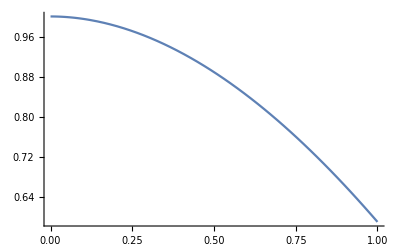

```mathematica
Plot[sol[x],{x,0,1}]
```

```mathematica
2(b)
```

```mathematica
LaplaceTransform[D[U[x,t],{t,2}],t,s]
```

s^2 LaplaceTransform[U[x,t],t,s]-s U[x,0]-U^(0,1)[x,0]

```mathematica
3
```

```mathematica
f[z_]:=(1+i)*x^3-(1-i)*y^3/;z≠0
f[z_]:=0;z=0
u[x_,y_]=x^3-y^3;
v[x_,y_]=x^3+y^3;
f[0]
```

0

```mathematica
mux=Limit[u[x,y]/.y->m*x,x->0]
mvx=Limit[v[x,y]/.y->m*x,x->0]
mu0=Limit[Limit[u[x,y],y->0],x->0]
mv0=Limit[Limit[v[x,y],y->0],x->0]
```

0

0

0

«1 more identical outputs»

```mathematica
mux+i*mvx
```

0

```mathematica
u0=u[x,0]/.x->0;
v0=v[x,0]/.x->0;
Subscript[u, x]=Limit[(u[x,0]-u0)/x,x->0]
Subscript[u, y]=Limit[(u[0,y]-u0)/y,y->0]
Subscript[v, x]=Limit[(v[x,0]-v0)/x,x->0]
Subscript[v, y]=Limit[(v[0,y]-v0)/y,y->0]
If[Subscript[u, x]==Subscript[v, y] && Subscript[v, x]==-Subscript[u, y],Print["Cauchy Riemann equations are satisfied"]]
```

1

-1

1

1

Cauchy Riemann equations are satisfied

```mathematica
Dfx=Limit[(u[x,y]+i*v[x,y]-0)/(x+i*y)/.y->x,x->0]
Df0=Limit[(u[x,y]+i*v[x,y]-0)/(x+i*y)/.y->0,x->0]
If[Dfx==Df0,Print["Derivative exists"],Dfx≠Df0,Print["Derivative does not exists"]]
```

i/(1+i)

1+i

Derivative does not exists

```mathematica
4(a)
```

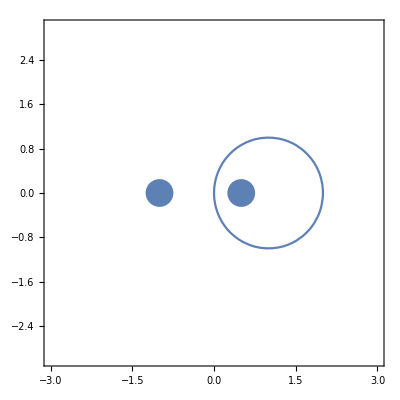

```mathematica
cir=ContourPlot[(x-1)^2+y^2==1,{x,-3,3},{y,-3,3},DisplayFunction->Identity];
lst={{-1,0},{1/2,0}};
pt=ListPlot[lst,PlotStyle->PointSize[0.05],DisplayFunction->Identity];
Show[{cir,pt},Axes->True,DisplayFunction->$DisplayFunction]
```

```mathematica
a1=pol[[3,1,2]];
r1=Residue[f[z],{z,a1}];
intgral=2*π*i*r1
```

(4 i π)/9

```mathematica
5)
```

```mathematica
Print["Iteration     Values           Error"   ]
f[x_]:=x^3-2x-5;x0=2.0;n=1;tol=0.0001;
x1=x0-f[x0]/f'[x0];error=x0-x1;
While[Abs[error]>tol,x1=x0-f[x0]/f'[x0];error=x0-x1;
Print["    ",n,"       ",PaddedForm[x1,{7,5}],"      ",PaddedForm[error,{7,5}]];n++;x0=x1]
Print["Hence the real root is = ",x1]
```

Iteration     Values           Error

1         2.10000       -0.10000

2         2.09457        0.00543

3         2.09455        0.00002

Hence the real root is = 2.09455

```mathematica
6)
```

```mathematica
Print["Iteration       x          y            z"]
x=0;y=0;z=0;
tol=0.0001;i=1;
While[Abs[4.0*x+3.0*y-24.0]>tol,x=1/4.0(24.0-3.0*y)//N;
y=1/4.0(30.0-3.0*x+z)//N;
z=1/4.0(-24.0+y)//N;
Print[i,PaddedForm[x,{15,3}],PaddedForm[y,{10,3}],PaddedForm[z,{10,3}]];i++]
```

Iteration       x          y            z

1            6.000       3.000      -5.250

2            3.750       3.375      -5.156

3            3.469       3.609      -5.098

4            3.293       3.756      -5.061

5            3.183       3.847      -5.038

6            3.114       3.905      -5.024

7            3.072       3.940      -5.015

8            3.045       3.963      -5.009

9            3.028       3.977      -5.006

10            3.017       3.985      -5.004

11            3.011       3.991      -5.002

12            3.007       3.994      -5.001

13            3.004       3.996      -5.001

14            3.003       3.998      -5.001

15            3.002       3.999      -5.000

16            3.001       3.999      -5.000

17            3.001       3.999      -5.000

18            3.000       4.000      -5.000

19            3.000       4.000      -5.000

20            3.000       4.000      -5.000

21            3.000       4.000      -5.000

22            3.000       4.000      -5.000

```mathematica
7)
```

```mathematica
sol2=DSolve[{y'[x]-y[x]+x^2-1==0,y[0]==0.5},y[x],x];
ex=sol2[[1,1,2]];
f[x_,y_]=y-x^2+1;
a=Input["Enter the left end point"];
b=Input["Enter the right end point"];
y0=Input["Enter the initial condition"];
n=Input["Enter the number of steps"];
h=(b-a)/n;
aa[0]=a;
bb[0]=y0;
For[i=1,i≤n,i++,
{
bb[i]=bb[i-1]+h*f[aa[i-1],bb[i-1]];
aa[i]=a+i*h;
}];
Print["   X_i          Approximation       Exact          Error"];
Print["-----------------------------------------------------------------------"];
s=Table[{aa[i],bb[i],ex/.{x->aa[i]},Abs[bb[i]-ex/.{x->aa[i]}]},{i,0,n}];
PaddedForm[TableForm[s]//N,{9,7}]
```

X_i          Approximation       Exact          Error

-----------------------------------------------------------------------

0.0000000 |   0.5000000 |   0.5000000 |   0.0000000
  0.2000000 |   0.8000000 |   0.8292986 |   0.0292986
  0.4000000 |   1.1520000 |   1.2140877 |   0.0620877
  0.6000000 |   1.5504000 |   1.6489406 |   0.0985406
  0.8000000 |   1.9884800 |   2.1272295 |   0.1387495
  1.0000000 |   2.4581760 |   2.6408591 |   0.1826831
  1.2000000 |   2.9498112 |   3.1799415 |   0.2301303
  1.4000000 |   3.4517734 |   3.7324000 |   0.2806266
  1.6000000 |   3.9501281 |   4.2834838 |   0.3333557
  1.8000000 |   4.4281538 |   4.8151763 |   0.3870225
  2.0000000 |   4.8657845 |   5.3054720 |   0.4396874

```mathematica
8)
```

```mathematica
n=Input["Enter the number of equation"];
For[i=1,i≤n,i++,For[j=1,j≤n+1,j++,a[i,j]=Input["Enter the coefficients(row wise)"];]];
s=Table[a[i,j],{i,1,n},{j,1,n+1}];
TableForm[s]
For[i=1,i≤n,i++,nn=a[i,i];For[j=i,j≤n+1,j++,a[i,j]=a[i,j]/nn;];
For[k=1,k≤n,k++,If[k≠i,mm=a[k,i];For[m=i,m≤n+1,m++,a[k,m]=a[k,m]-mm*a[i,m];];];];];
For[k=1;Print["Gauss Jordan Method "];Print["Solutions"],k≤n,k++,Print[a[k,n+1]//N]];
```

5 | -2 | 1 | 4
7 | 1 | -5 | 8
3 | 7 | 4 | 10

Gauss Jordan Method

Solutions

1.11927

0.868502

0.140673